Approximation of (ϕ, θ)-values at ESS for long periods between transfers
for the system with arbitrium signalling + regulation

If the interval between transfers is sufficiently long, the strain distribution in the free phage population will resemble the distribution in the lysogen compartment. The strain distribution in the lysogen compartment is determined in the phase in which lysogens are formed by infection of susceptibles when S still > 0.

Let every phage strain be characterised by two values:
τ 	time at which the arbitrium concentration becomes higher than the phage’s threshold value θ
ϕ	lysogenisation propensity when time > τ (arbitrium concentration > θ)

Simplifying assumptions:
- Assume that bacterial dynamics are much slower than phage infection dynamics.
- Assume lysogen growth (due to infections) during the initial phase is small, and hence N = approx S.
- Assume that during the initial phase, S is fixed and then drops to 0.
Let T be the duration of the initial phase (for which S=1). [T is a function of ϕ and τ.]
Because phages need to produce lysogens before S=0, it is safe to say that τ < T.
Scale time by β (i.e. divide all rates by β), and define η = 1 - a/β.
Then for the period t = 0 - τ, the system is decribed by:
dL / dt = 0
dP / dt = η P
Hence:
P(t) = P0 Exp[ η t ]
L(t) = 0
For the period t = τ - T, the system is described by:
dL/dt = ϕ P
dP/dt = (1 - ϕ)P - a/β P
Hence (using L(τ) = 0 and P(τ) = Exp[η τ]):
P(t) = P0 Exp[ητ + (η - ϕ)t]
L(t) = ϕ P0 Exp[ητ]/(η - ϕ) (Exp[(η - ϕ)t] - Exp[(η - ϕ)τ])

Standard Parameters for plotting:

```mathematica
params = {β-> 20, a -> 10,P0-> 0.0001,τ-> 10,T -> 20}
```

{β→20,a→10,P0→0.0001,τ→10,T→20}

```mathematica
paramsnoP0 = {β-> 20, a -> 10,τ-> 10,T -> 20}
```

{β→20,a→10,τ→10,T→20}

```mathematica
η = 1 - a/β;
```

```mathematica
assum = {β>0,a>0,P0>0,τ>0,T>0,0≤ ϕ≤ 1,β>a, T>τ};
```

Plot Log(P) and Log(L) as functions of time,  for different values of ϕ

Piecewise[{{ⅇ^(t (1-a/β)) P0, t≤τ}, {ⅇ^((1-a/β) τ+(t-τ) (1-a/β-ϕ)) P0, t>τ}, {0, True}}]

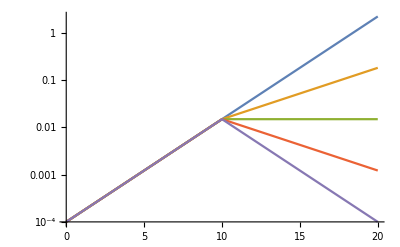

```mathematica
P1[ϕ_,τ_,P0_,t_] := P0 Exp[η t];
P[ϕ_,τ_,P0_,t_] := P0 Exp[η τ + (η-ϕ)(t-τ)];
Pfull[ϕ_,τ_,P0_,t_] := Piecewise[{{P1[ϕ,τ,P0,t],t ≤ τ},{P[ϕ,τ,P0,t],t>τ}}]
Pfull[ϕ,τ,P0,t]
LogPlot[{Pfull[0,τ,P0,t]/.params,Pfull[0.25,τ,P0,t]/.params,Pfull[0.5,τ,P0,t]/.params,Pfull[0.75,τ,P0,t]/.params,Pfull[1,τ,P0,t]/.params},{t,0,T/.params}]
```

The number of lysogens at time t > τ is now given by:

```mathematica
L[ϕ_, τ_, P0_,t_]=FullSimplify[ϕ Integrate[P[ϕ, τ, P0, t2], {t2, τ, t}]]
```

((ⅇ^(τ-(a τ)/β)-ⅇ^(t-(a t)/β-t ϕ+τ ϕ)) P0 β ϕ)/(a+β (-1+ϕ))

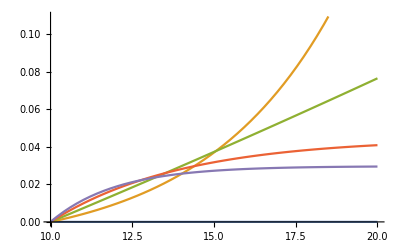

```mathematica
Plot[{L[0,τ,P0,t]/.params,L[0.25,τ,P0,t]/.params,L[0.49,τ,P0,t]/.params,L[0.75,τ,P0,t]/.params,L[1,τ,P0,t]/.params},{t,τ /. params,T/.params}]
```

Given T, what genotype (ϕ*, τ*) optimizes L(T)?

Calculating the optimal ϕ is a little complicated, so we first optimize τ and only after that ϕ at the optimal τ.

Plot the number of lysogens at time T as a function of τ:

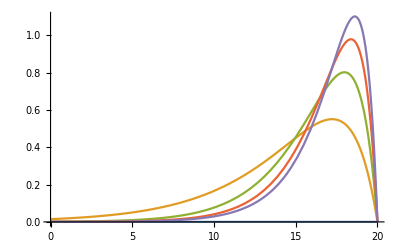

```mathematica
Plot[{L[0,t,P0,T]/.params,L[0.25,t,P0,T]/.params,L[0.49,t,P0,T]/.params,L[0.75,t,P0,T]/.params,L[1,t,P0,T]/.params}, {t,0,20}]
```

Derivative of number of lysogens at time T w.r.t. τ :

```mathematica
derLτ[ϕ_, τ_,P0_, T_]=FullSimplify[D[L[ϕ, τ,P0, T], τ]]
```

(P0 β ϕ (ⅇ^(τ-(a τ)/β) (1-a/β)-ⅇ^(T-(a T)/β-T ϕ+τ ϕ) ϕ))/(a+β (-1+ϕ))

The optimal τ becomes:

```mathematica
optτ[ϕ_, T_]=FullSimplify[ τ /. Solve[derLτ[ϕ, τ,P0, T]==0, τ][[1]]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

T+(β Log[(-a+β)/(β ϕ)])/(a+β (-1+ϕ))

To get an idea of the optimal ϕ given optimal τ, plot the number of lysogens at time T as a function of ϕ:

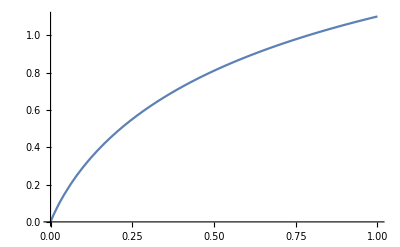

```mathematica
Plot[L[ϕ,optτ[ϕ,T],P0,T]/.params,{ϕ,0,1}]
```

It seems like ϕ* = 1 is the optimal value :)
To formally find the optimal ϕ*, consider the derivative of the number of lysogens at time T w.r.t. ϕm:

```mathematica
derLϕ[ϕ_,τ_, P0_, T_]=FullSimplify[D[L[ϕ, τ,P0, T], ϕ]]
```

(ⅇ^(-(a (T+τ))/β-T ϕ) P0 β (ⅇ^((a T)/β+τ+T ϕ) (a-β)+ⅇ^(T+(a τ)/β+τ ϕ) (β+β (T-τ) (-1+ϕ) ϕ+a (-1+T ϕ-τ ϕ))))/(a+β (-1+ϕ))^2

At the optimal τ, this amounts to:

```mathematica
derLϕoptτ[ϕ_, P0_,T_]=FullSimplify[derLϕ[ϕ,optτ[ϕ,T],P0, T]]
```

(ⅇ^(T-(2 a T)/β-T ϕ) P0 β ((-a+β)/(β ϕ))^(-a/(a+β (-1+ϕ))) (ⅇ^(T (a/β+ϕ)) (a-β) ((-a+β)/(β ϕ))^(β/(a+β (-1+ϕ)))-ⅇ^((a+β ϕ) (T/β+Log[(-a+β)/(β ϕ)]/(a+β (-1+ϕ)))) (a-β+β ϕ Log[(-a+β)/(β ϕ)])))/(a+β (-1+ϕ))^2

Now, we would like to show that this derivative is always positive for 0 <= ϕ <= 1.

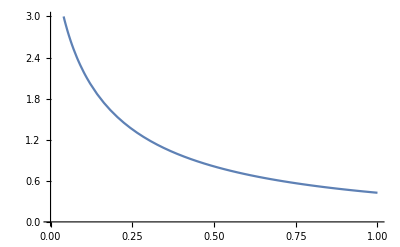

```mathematica
Plot[derLϕoptτ[ϕ,P0,T]/.params,{ϕ,0,1}, PlotRange->{0,3}]
```

```mathematica
Solve[derLϕoptτ[ϕ,P0,T]== 0, ϕ]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{}

So, mathematica cannot find a value for which the derivative is zero (i.e. it doesn’t exist?). That would mean that the derivative is always positive or negative. If we consider the limits for ϕ -> 0 and ϕ -> η (where the denominator -> 0), we see:

```mathematica
Limit[derLϕoptτ[ϕ,P0,T],ϕ-> 0]
```

Limit[(ⅇ^(T-(2 a T)/β-T ϕ) P0 β ((-a+β)/(β ϕ))^(-a/(a+β (-1+ϕ))) (ⅇ^(T (a/β+ϕ)) (a-β) ((-a+β)/(β ϕ))^(β/(a+β (-1+ϕ)))-ⅇ^((a+β ϕ) (T/β+Log[(-a+β)/(β ϕ)]/(a+β (-1+ϕ)))) (a-β+β ϕ Log[(-a+β)/(β ϕ)])))/(a+β (-1+ϕ))^2,ϕ→0]

```mathematica
Limit[derLϕoptτ[ϕ,P0,T],ϕ-> η]
```

-(ⅇ^(-1+T-(a T)/β) P0 β)/(2 (a-β))

Since β > a (necessary assumption to get exponential growth of phages), both of these limits are positive. Hence, the derivative is always positive (???)

Here : room for improvement. Is this enough to say that we can show analytically that derLϕoptτ is always > 0?

The plots above suggest that dL/dϕ is always positive on [0,1], and hence we for now conclude that for any given T, ϕ* = 1.
The corresponding τ* then is:

```mathematica
optτ[1,T]
```

T+(β Log[(-a+β)/β])/a

or in terms of η = 1 - a/β: 
τ* = T + Log[η] / (1 - η)

REMEMBER  that all these times (T, τ) are in transformed time units (time scaled with infection rate β)

Finding T(ϕ, τ)

The next step is to determine how the time T, at which the S population collapses, depends on ϕ ( = 1) an τ.

Define T as the time at which a given number of infections has taken place (i.e., as the time at which S has been depleted by some value). Since S=1 at carrying capacity, a reasonable estimate of T would be to ask when a total of 1 (measured in “carrying capacities”) infections has taken place. Given t > τ, the number of infections that has taken place is given by
J(t) = Integral 0 to τ [ P0 Exp[η t]] dt + Integral τ to t[P(τ)] dt = 1 / η P0 (Exp[η τ] - 1) + P(τ)(t - τ) =  P0 / η ( Exp[η τ](1+η (t - τ)) - 1 )

```mathematica
J[t_, τ_, P0_] = Integrate[P1[ϕ,τ,P0,x],{x,0,τ}] + Integrate[P[ϕ,τ,P0,x]/.{ϕ-> 1},{x,τ,t}]
```

(ⅇ^τ (-ⅇ^(-(a t)/β)+ⅇ^(-(a τ)/β)) P0 β)/a+((-1+ⅇ^(τ-(a τ)/β)) P0 β)/(-a+β)

J (T) = 1 seems reasonable (although this will slightly overestimate T, because it assumes that all susceptible cells have gotten infected).  We know that we should always have τ < T. Hence we find an upper bound on τ:

```mathematica
Jnolysogen[t_,P0_] = Integrate[P1[ϕ,τ,P0,x],{x,0,t}]
τupp[P0_] = τ/.(Assuming[assum,Simplify[Solve[Jnolysogen[τ,P0]==1,τ,Reals]]])[[1,1]]
```

((-1+ⅇ^(t-(a t)/β)) P0 β)/(-a+β)

(β Log[(P0 β)/(-a+β+P0 β)])/(a-β)

Setting J (T) = 1 :

```mathematica
Assuming[Join[assum,{T<τmax[P0]}],Simplify[Solve[J[T,τ,P0] == 1, T]]]
```

{{T→ConditionalExpression[(β (2 ⅈ π C[1]+Log[-(ⅇ^(τ+(a τ)/β) P0 (a-β) β)/(a^2 ⅇ^((a τ)/β)-a ⅇ^((a τ)/β) (1+P0) β+ⅇ^τ P0 β^2)]))/a,C[1]∈Integers]}}

```mathematica
Solve[J[T,τ,P0] == 1,T, Reals]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[(ⅇ^τ (-ⅇ^(-(a T)/β)+ⅇ^(-(a τ)/β)) P0 β)/a+((-1+ⅇ^(τ-(a τ)/β)) P0 β)/(-a+β)==1,T,Reals]

This doesn’t work (maybe need to put extra conditions on logarithm to be positive?)...
On the other hand, we are not that interested in the expression for T, but more in the value for τ that solves J(T(τ)) == 1 with τ optimal given T. We know that

```mathematica
Tatoptτ[ϕ_,τ_] =T/.(Solve[optτ[ϕ,T]==τ,T][[1,1]])
Tatoptτ[1,τ]
```

(a τ-β τ+β τ ϕ-β Log[(-a+β)/(β ϕ)])/(a-β+β ϕ)

(a τ-β Log[(-a+β)/β])/a

Substituting into J(T) = 1:

```mathematica
Solve[J[Tatoptτ[1,τ],τ,P0]==1,τ]
finaloptτ[P0_] = τ/.(%[[1,1]])
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{τ→(β Log[-(P0 (a-2 β))/(-a+β+P0 β)])/(a-β)}}

(β Log[-(P0 (a-2 β))/(-a+β+P0 β)])/(a-β)

Plot the optimal τ as a function of P0.
(NB: τ is here still given in the transformed time units (transformed by factor β))

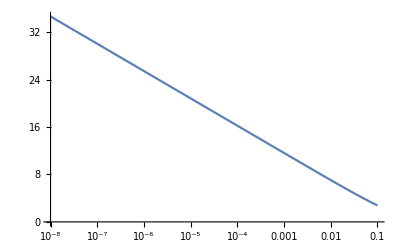

```mathematica
LogLinearPlot[finaloptτ[P0]/.paramsnoP0,{P0,10^(-8),0.1}]
```

In the original time units:

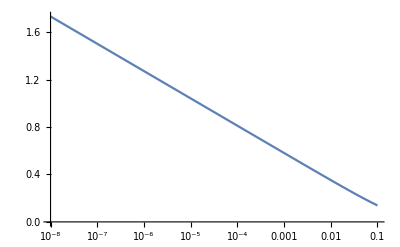

```mathematica
LogLinearPlot[β^-1 finaloptτ[P0]/.paramsnoP0,{P0,10^(-8),0.1}]
```

Connect the “time threshold” τ* to arbitrium concentration

Phages do not have a timer, but sense the arbitrium concentration A(t), and switch behaviour (ϕ = 0 -> ϕ = 1) when A > threshold concentration θ. The final question to answer is therefore: what is A(τ*)?

Under the assumption (that we frequently make) that arbitrium is not produced by lysogens and not spontaneously degraded (but is taken up by cells and degraded in the cells):
dA / dt = β S P - u A (S + L)
which in the situation considered here (S = 1, L = 0, transformed time units) is
dA / dt = P - u/β A,
with P(t) = P0 Exp[η t] for 0 < t <τ, 
(and P(t) = P0 Exp[η τ + (η - 1) (t - τ)] for τ < t < T, but this range is not relevant here).
To find A(t), we need to solve this differential equation:

```mathematica
sol = DSolve[{A'[t] == P0 Exp[η t] - (u/β) A[t], A[0] == 0}, A[t],t]
A[t_] = A[t]/.sol[[1]]
```

{{A[t]→(ⅇ^(-(t u)/β) (-1+ⅇ^((t (-a+u+β))/β)) P0 β)/(-a+u+β)}}

(ⅇ^(-(t u)/β) (-1+ⅇ^((t (-a+u+β))/β)) P0 β)/(-a+u+β)

Then, we can easily find A(τ):

```mathematica
sol = FullSimplify[A[finaloptτ[P0]]]
```

-(β (-a+β+P0 β+P0 (a-2 β) (-(P0 (a-2 β))/(-a+β+P0 β))^(u/(-a+β))))/((a-2 β) (-a+u+β))

```mathematica
optθ[P0_,u_] = sol
```

-(β (-a+β+P0 β+P0 (a-2 β) (-(P0 (a-2 β))/(-a+β+P0 β))^(u/(-a+β))))/((a-2 β) (-a+u+β))

Plotting the threshold value as a function of P0:

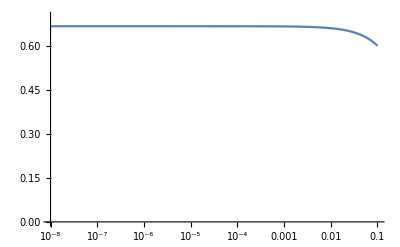

```mathematica
LogLinearPlot[optθ[P0,u]/.Join[paramsnoP0,{u-> 0}],{P0,10^(-8),0.1}, PlotRange-> {0,0.7}]
```

Plotting the threshold value as a function of arbitrium uptake u:

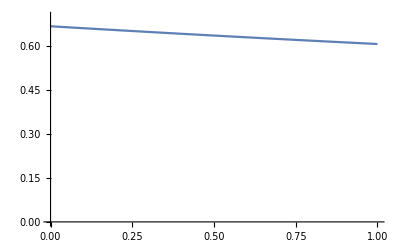

```mathematica
Plot[optθ[P0,u]/.params,{u,0,1},PlotRange->{0,0.7}]
```

Probeersel

```mathematica
p0[α_,d_,δ_,a_] := d α / (δ+a)
optθtest[β_,α_,a_,d_,δ_,u_]:= (((1 - a/β) + p0[α,d,δ,a] - p0[α,d,δ,a]*(1+(1 - a/β))*(((1+(1 - a/β))p0[α,d,δ,a])/((1 - a/β)+p0[α,d,δ,a]))^(u/(β (1 - a/β))))/((1+(1 - a/β))((1 - a/β)+u/β)))
optθtest[β,α,a,d,δ,u]
```

(1-a/β+(d α)/(a+δ)-(d α (2-a/β) ((d α (2-a/β))/((a+δ) (1-a/β+(d α)/(a+δ))))^(u/((1-a/β) β)))/(a+δ))/((2-a/β) (1-a/β+u/β))

```mathematica
optθtest[20,0.001,10,0.01,0.01,0.1]
```

0.660066

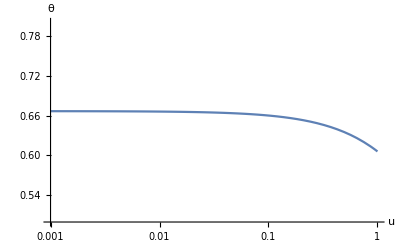

```mathematica
LogLinearPlot[optθtest[20,0.001,10,0.01,0.01,u],{u,0.001,1},PlotRange->{0.5,0.8},AxesLabel->{u,θ}]
```

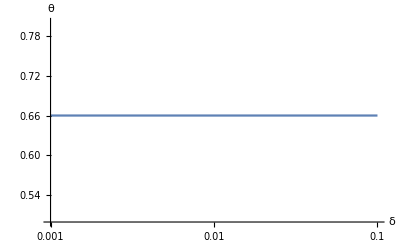

```mathematica
LogLinearPlot[optθtest[20,0.001,10,0.01,δ,0.1],{δ,0.001,0.1},PlotRange->{0.5,0.8},AxesLabel->{δ,θ}]
```

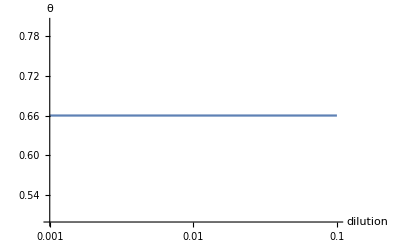

```mathematica
LogLinearPlot[optθtest[20,0.001,10,d,0.01,0.1],{d,0.001,0.1},PlotRange->{0.5,0.8},AxesLabel->{dilution,θ}]
```

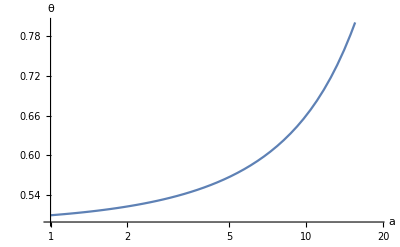

```mathematica
LogLinearPlot[optθtest[20,0.001,a,0.01,0.01,0.1],{a,1,19},PlotRange->{0.5,0.8},AxesLabel->{a,θ}]
```

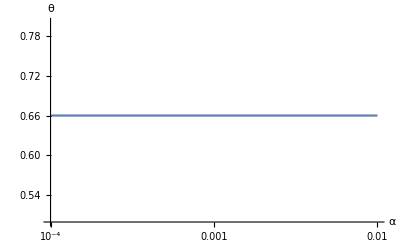

```mathematica
LogLinearPlot[optθtest[20,α,10,0.01,0.01,0.1],{α,0.0001,0.01},PlotRange->{0.5,0.8},AxesLabel->{α,θ}]
```

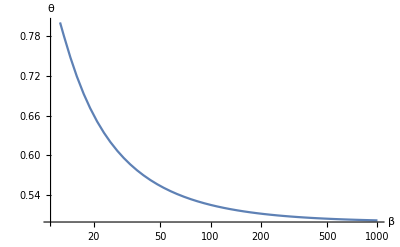

```mathematica
LogLinearPlot[optθtest[β,0.001,10,0.01,0.01,0.1],{β,11,1000},PlotRange->{0.5,0.8},AxesLabel->{β,θ}]
```

Plot how the “simple” prediction depends on B(β/a):

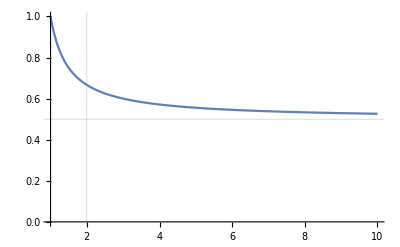

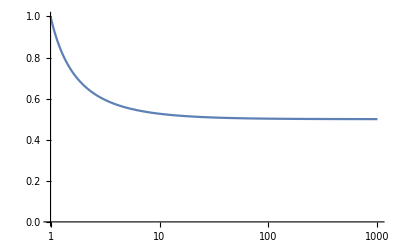

```mathematica
θpred[x_] := x/(2x-1)
Plot[θpred[x],{x,1,10},PlotRange->{{1,10},{0,1}}, GridLines->{{2},{0.5}}]
LogLinearPlot[θpred[x],{x,1,1000},PlotRange->{{1,1000},{0,1}}, GridLines->{{2},{0.5}}]
```